# Physics through Computational Thinking

## Damped Oscillators

Auditya Sharma and Ambar Jain

Dept. of Physics, IISER Bhopal

Outline

In this video you will

work through the examples of damped oscillator

### Simple Harmonic Oscillator

A simple harmonic oscillator is a dynamical system that obeys the following equation of motion:

x^(..)+ω^2 x=0

Solution of this equation is given by

x(t)=A cos(ω t)+B sin(ω t)
x(t)=C ⅇ^(ⅈ ω t)+D ⅇ^(-ⅈ ω t)
x(t)=F cos(ω t+ϕ)
x(t)=G sin(ω t+ψ)

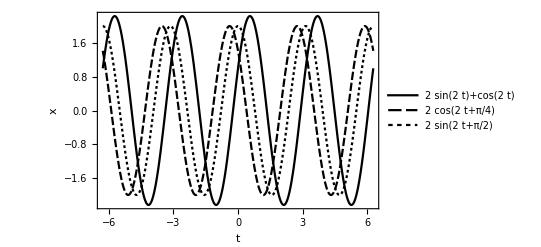

```mathematica
Plot[{2 Sin[2 t]+Cos[2t],2Cos[2t+π/4],2Sin[2t+π/2]},{t,-2π,2π},PlotLegends->"Expressions",Frame->True,FrameLabel->{"t","x"}]
```

### Damped Oscillator

Consider the LC circuit we just discussed. Usually circuit components always have some resistance, such as connecting cables, even the inductor and capacitor has some resistance.

Lets add a resistor to our circuit and using Kirchhoff’s law work out the equation again.

-Graphics-

L ⅆI/ⅆt+Q/C+I R=0
⇒ (ⅆ^2 Q)/(ⅆ t^2)=-Q/(L C)-R/L ⅆQ/ⅆt

We can think of this equation in terms of mechanics, thinking of Q as displacement.

-Q/(L C) provides the restoring force, causing the oscillation

-(R/L)  ⅆQ/ⅆt drags down the “acceleration of the charge” (ⅆ^2 Q/ⅆ t^2) as its always opposite to “speed of charge” (ⅆQ/ⅆt).

It is anticipated that Joule heating of the resistor will reduce the energy from the system therefore will cause the oscillation to damp down.

### Problem

Working in groups of nine (entire table) on the white board next to you, solve the following problems.

(a) Identify the time scales in this problem and the role they play?

(b) At what rate do you expect the average energy of the capacitor is reducing?

(c) Try the solution of the form given below to show that it satisfies the equation of motion. Determine the constants α and β.

Q(t)=A ⅇ^(-α t)cos(β t+ϕ)

(d) Using the initial conditions Q(0)=Q_0 and Q̇(0)=0, find the constants of integration.

(e) At what rate average energy of the capacitor is decreasing, assuming a very small resistance in the circuit?

### Time Scales in Damped Spring Mass System

-Graphics-

(a) Consider the set-up shown in the figure above, where each spring has a spring constant k and natural length a_0. Earlier, we ignored friction in this problem. Now, assuming the coefficient of friction between the block and the surface is μ, obtain the equation of motion.

(b) Obtain the time scales in this problem? Can you find the time scale associated with oscillation and a time scale associated with damping?

(c) Assuming small friction so that the damping is happening at a very slow rate, estimate the rate at which energy in the oscillator is changing and the rate at which amplitude is changing.

### Solution

z^(..)=-(2k)/mz-μ g sgn(ż)

Based on Dimensional Analysis we get the following,

T_osc∼2π √(m/(2k))
T_damping∼2π √(a_1/(μ g))

Using naive dimensional analysis we may estimate

1/E ⅆE/ⅆt∼1/T_damping~√((μ g)/a_1)∝1/(√a_1)

Alternately, we can also estimate 1/E ⅆE/ⅆt as

1/E ⅆE/ⅆt∼1/E ΔE/Δt∼ 1/(1/2 k a_1^2) (4 μ m g a_1)/T_osc=1/(1/2 k a_1^2) (4 μ m g a_1)/(2π √(m/(2k)))∝1/a_1

These are two different results, How do we know which one is correct. For validating it let’s find out what’s happening with the amplitude. For slow damping, using E=1/2 k a_1^2, we also  get

1/E ⅆE/ⅆt=2((ȧ)_1)/a_1

Therefore we have two different claims for how amplitude changes, one from naive dimensional analysis and another using physics input:

naive Dimensional Analysis: (ȧ)_1∝√a_1

using physics of damping:   (ȧ)_1∝const

Let’s find out which one is correct, by solving this system numerically.

### Validating using Numerical Solution

For the non-dimensionalized version with suitable small value of μ, the system’s equation will become

z^(..)=-z-0.02 sgn(ż)

Solving it numerically we see that instantaneous amplitude a_1 decreases linearly, thus (ȧ)_1=const. :

```mathematica
numsol=NDSolve[{z''[t]==-z[t]-0.02Sign[z'[t]],z[0]==1,z'[0]==0},z[t],{t,0,100}]
```

{{z[t]→InterpolatingFunction[…][t]}}

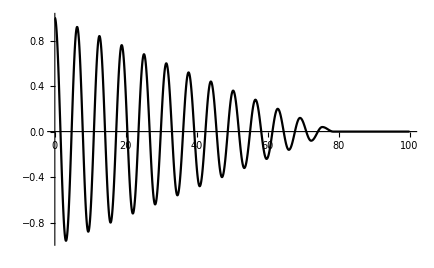

```mathematica
Plot[z[t]/.numsol,{t,0,100}]
```